# Data generation

## TODO

## Data format

Artificial data generation for clulstering varidity.

Data structire:
<Model and annotation>
;
<Dimension>[\tab]<Number of clusters>[\tab]<Number of samples>[\tab]<Number of background points>
;
<Cluster centers (model): matrix with tab delimiter>
;
<Samples: matrix with tab delimiter>
;

## Preparation

```mathematica
(*dir="/Users/amanokou/gitsrc/"*)
```

```mathematica
(*dir="/Users/kouamano/gitsrc/"*)
```

```mathematica
dir="/home/kamano/gitsrc/"
```

/home/kamano/gitsrc/

```mathematica
Get[dir<>"MATH_SCRIPT/SCRIPTS/polar.txt"]
```

```mathematica
SetDirectory[dir<>"ClusteringAdequation/generative-data"]
```

/home/kamano/gitsrc/ClusteringAdequation/generative-data

## Programs

```mathematica
strDataToExportStr[n_]:=StringJoin[Riffle[{anntS[n],dimS[n],centersS[n],samplesS[n]},";\n"]]
```

```mathematica
distanceMat[mat_]:=Module[
{n},
n=Length[mat];
Table[EuclideanDistance[mat[[i]],mat[[j]]],{i,n},{j,n}]
]
```

## 2D

### data 1 (general)

```mathematica
id=1
```

1

```mathematica
anntS[id]="Model: central random, circles, one radius, triangle.\n"
```

Model: central random, circles, one radius, triangle.

```mathematica
dim[id]=2;
numClass[id]=3;
numSample[id]={100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{0}

```mathematica
centers[id]=Map[polarToxy[N[{1,#}]]&,Table[2Pi/numClass[id] n,{n,0,2}]]
```

{{1.,0.},{-0.5,0.866025},{-0.5,-0.866025}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

1.	0.
-0.4999999999999998	0.8660254037844387
-0.5000000000000004	-0.8660254037844384

```mathematica
distanceMat[centers[id]]
```

{{0.,1.73205,1.73205},{1.73205,0.,1.73205},{1.73205,1.73205,0.}}

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]]]/(numClass[id]^2-numClass[id])
```

1.73205

```mathematica
samples[id]=Table[Map[#+centers[id][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[id]/2}],RandomReal[{0,2Pi}]}],{numSample[id][[n]]}]],{n,numClass[id]}];
```

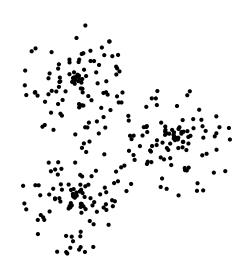

```mathematica
Graphics[Map[Point[#]&,samples[id],{2}]]
```

```mathematica
samplesS[id]=ExportString[Flatten[samples[id],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id],1]]
```

{0.012209,-0.0375538}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id],1]]]
```

1.02716

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id]]
```

{{0.960096,-0.0283095},{-0.448982,0.809062},{-0.474486,-0.893414}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.422909,0.441816,0.436845}

Export 3f iles:

```mathematica
Export["data1.tsv",strDataToExportStr[id],"String"]
```

data1.tsv

```mathematica
Export["data1.ans.totalR",totalR[id],"Table"]
```

data1.ans.totalR

```mathematica
Export["data1.ans.clRs",clRs[id],"Table"]
```

data1.ans.clRs

### data 2 (unbalanced)

```mathematica
id=2
```

2

```mathematica
anntS[id]="Model: unbalanced central random, circles, radiuses.\n"
```

Model: unbalanced central random, circles, radiuses.

```mathematica
dim[id]=2;
numClass[id]=3;
numSample[id]={200,100,50};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

2	3	{200, 100, 50}	{0}

```mathematica
centers[id]={{0,0},{0.5,-1},{-0.5,-0.75}}
```

{{0,0},{0.5,-1},{-0.5,-0.75}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

0	0
0.5	-1
-0.5	-0.75

```mathematica
distanceMat[centers[id]]
```

{{0,1.11803,0.901388},{1.11803,0.,1.03078},{0.901388,1.03078,0.}}

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]]]/(numClass[id]^2-numClass[id])
```

1.01673

```mathematica
radius[id]={distMean[id]*0.6,distMean[id]*0.4,distMean[id]*0.2}
```

{0.61004,0.406693,0.203347}

```mathematica
samples[id]=Table[Map[#+centers[id][[n]]&,Table[polarToxy[{RandomReal[{0,radius[id][[n]]}],RandomReal[{0,2Pi}]}],{numSample[id][[n]]}]],{n,numClass[id]}];
```

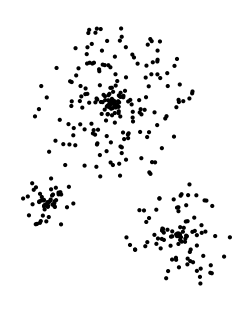

```mathematica
Graphics[Map[Point[#]&,samples[id],{2}]]
```

```mathematica
samplesS[id]=ExportString[Flatten[samples[id],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=2
```

2

```mathematica
totalCenter[id]=Mean[Flatten[samples[id],1]]
```

{0.0795455,-0.383186}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id],1]]]
```

0.595451

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id]]
```

{{0.0152797,0.0181141},{0.498449,-1.00172},{-0.501198,-0.751326}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.299258,0.183992,0.0984645}

```mathematica
Export["data2.tsv",strDataToExportStr[2],"String"]
```

data2.tsv

```mathematica
Export["data2.ans.totalR",totalR[id],"Table"]
```

data2.ans.totalR

```mathematica
Export["data2.ans.clRs",clRs[id],"Table"]
```

data2.ans.clRs

### data 4 (sub class)

```mathematica
anntS[4]="Model: central random , circles, one radius, subclusters.\n"
```

Model: central random , circles, one radius, subclusters.

```mathematica
dim[4]=2;
numClass[4]=4;
numSample[4]={100,100,100,100};
numBG[4]={0};
```

```mathematica
dimS[4]=StringJoin[Riffle[{ToString[dim[4]],ToString[numClass[4]],ToString[numSample[4]],ToString[numBG[4]]},"\t"],"\n"]
```

2	4	{100, 100, 100, 100}	{0}

```mathematica
centers[4]={{2,1},{2,-1},{-2,1},{-2,-1}}
```

{{2,1},{2,-1},{-2,1},{-2,-1}}

```mathematica
centersS[4]=ExportString[centers[4],"TSV"]<>"\n"
```

2	1
2	-1
-2	1
-2	-1

```mathematica
distMean[4]=Tr[Flatten[distanceMat[centers[4]]//N]]/(numClass[4]^2-numClass[4])
```

3.49071

```mathematica
samples[4,"class"]=Table[Map[#+centers[4][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[4]/4}],RandomReal[{0,2Pi}]}],{numSample[4][[n]]}]],{n,numClass[4]}];
```

```mathematica
maxmin[4]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[4,"class"],1]]]
```

{{2.78681,-2.80275},{1.78202,-1.84985}}

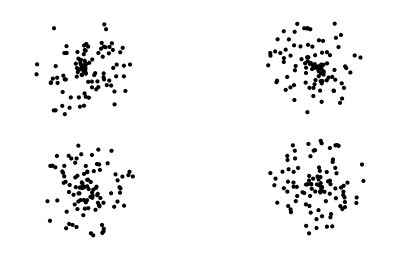

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[4,"class"],1]]]
```

```mathematica
samplesS[4]=ExportString[Flatten[samples[4,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=4
```

4

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{0.00790007,0.0000207384}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

2.22684

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{1.92303,1.06521},{1.98538,-0.986793},{-1.94575,0.976077},{-1.93106,-1.05441}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.408557,0.44878,0.410619,0.423901}

```mathematica
Export["data4.tsv",strDataToExportStr[4],"String"]
```

data4.tsv

```mathematica
Export["data4.ans.totalR",totalR[id],"Table"]
```

data4.ans.totalR

```mathematica
Export["data4.ans.clRs",clRs[id],"Table"]
```

data4.ans.clRs

### data 5 (ring + disc)

```mathematica
anntS[5]="Model: central random , disc + ring.\n"
```

Model: central random , disc + ring.

```mathematica
dim[5]=2;
numClass[5]=2;
numSample[5]={100,200};
numBG[5]={0};
```

```mathematica
dimS[5]=StringJoin[Riffle[{ToString[dim[5]],ToString[numClass[5]],ToString[numSample[5]],ToString[numBG[5]]},"\t"],"\n"]
```

2	2	{100, 200}	{0}

```mathematica
centers[5]={{0,0},{0,0}}
```

{{0,0},{0,0}}

```mathematica
centersS[5]=ExportString[centers[5],"TSV"]<>"\n"
```

0	0
0	0

```mathematica
samples[5,"disc"]=Map[polarToxy[#]&,Table[{RandomReal[{0,1}],RandomReal[{0,2 Pi}]},{numSample[5][[1]]}]];
```

```mathematica
samples[5,"ring"]=Map[polarToxy[#]&,Table[{RandomReal[{1.5,2}],RandomReal[{0,2 Pi}]},{numSample[5][[2]]}]];
```

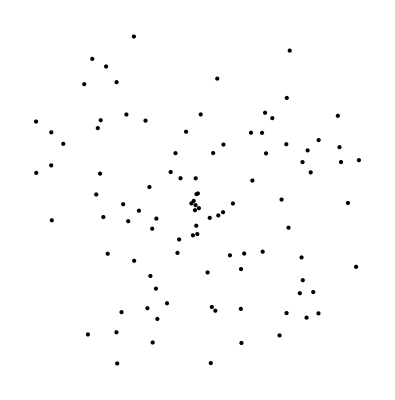

```mathematica
Graphics[Map[Point[#]&,samples[5,"disc"]]]
```

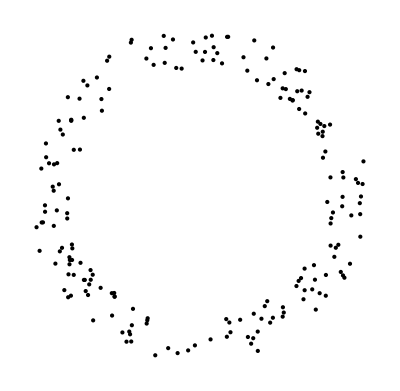

```mathematica
Graphics[Map[Point[#]&,samples[5,"ring"]]]
```

```mathematica
samples[5,"class"]=List[samples[5,"disc"],samples[5,"ring"]];
```

```mathematica
(*samplesS[1]=ExportString[Flatten[samples[1],1],"TSV"]<>"\n";*)
```

```mathematica
samplesS[5]=ExportString[Flatten[samples[5,"class"],1],"TSV"]<>"\n";
```

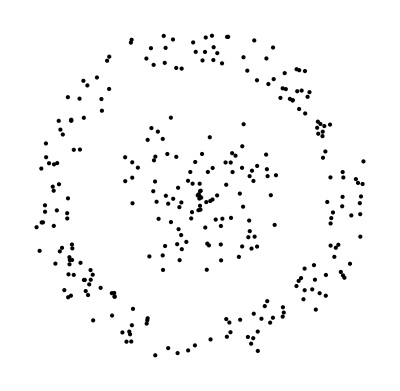

```mathematica
Map[Point[#]&,samples[5,"class"]]//Graphics
```

全サンプルの平均半径

```mathematica
id=5
```

5

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{0.0149103,-0.0388029}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.34373

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.0417488,-0.0281593},{0.00149102,-0.0441247}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.553968,1.7386}

```mathematica
Export["data5.tsv",strDataToExportStr[5],"String"]
```

data5.tsv

```mathematica
Export["data5.ans.totalR",totalR[id],"Table"]
```

data5.ans.totalR

```mathematica
Export["data5.ans.clRs",clRs[id],"Table"]
```

data5.ans.clRs

### data 6 (spiral)

```mathematica
anntS[6]="Model: spiral x 3.\n"
```

Model: spiral x 3.

```mathematica
dim[6]=2;
numClass[6]=3;
numSample[6]={100,100,100};
numBG[6]={0};
```

```mathematica
dimS[6]=StringJoin[Riffle[{ToString[dim[6]],ToString[numClass[6]],ToString[numSample[6]],ToString[numBG[6]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{0}

```mathematica
origins[6]={{0,0},{0,0},{0,0}}
```

{{0,0},{0,0},{0,0}}

```mathematica
(samples[6,0]=Map[polarToxy[#]&,Table[{r,3r},{r,0.5,3-0.02,0.025}]])//Length
```

100

```mathematica
center[6,0]=Mean[samples[6,0]]
```

{0.0684864,0.339278}

```mathematica
(samples[6,1]=Map[polarToxy[#]&,Table[{r,3r+(2Pi/3)},{r,0.5,3-0.02,0.025}]])//Length
```

100

```mathematica
center[6,1]=Mean[samples[6,1]]
```

{-0.328066,-0.110328}

```mathematica
(samples[6,2]=Map[polarToxy[#]&,Table[{r,3r+(4Pi/3)},{r,0.5,3-0.02,0.025}]])//Length
```

100

```mathematica
center[6,2]=Mean[samples[6,2]]
```

{0.25958,-0.22895}

```mathematica
centers[6]={center[6,0],center[6,1],center[6,2]}
```

{{0.0684864,0.339278},{-0.328066,-0.110328},{0.25958,-0.22895}}

```mathematica
centersS[6]=ExportString[centers[6],"TSV"]<>"\n"
```

0.06848640517315346	0.3392778825308757
-0.3280664678005077	-0.11032797457161272
0.25958006262735384	-0.22894990795926298

```mathematica
samples[6,"class"]=List[samples[6,0],samples[6,1],samples[6,2]];
```

```mathematica
samplesS[6]=ExportString[Flatten[samples[6,"class"],1],"TSV"]<>"\n";
```

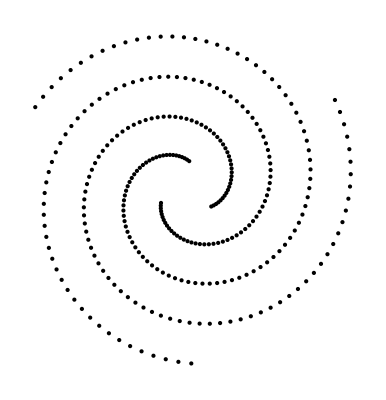

```mathematica
Map[Point[#]&,samples[6,"class"]]//Graphics
```

全サンプルの平均半径

```mathematica
id=6
```

6

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-1.12503×10^-16,4.81097×10^-17}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.7375

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.0684864,0.339278},{-0.328066,-0.110328},{0.25958,-0.22895}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{1.71971,1.71971,1.71971}

```mathematica
Export["data6.tsv",strDataToExportStr[6],"String"]
```

data6.tsv

```mathematica
Export["data6.ans.totalR",totalR[id],"Table"]
```

data6.ans.totalR

```mathematica
Export["data6.ans.clRs",clRs[id],"Table"]
```

data6.ans.clRs

## Noisy

### data 3 (noisy)

```mathematica
anntS[3]="Model: central random + noise, circles, one radius, triangle.\n"
```

Model: central random + noise, circles, one radius, triangle.

```mathematica
dim[3]=2;
numClass[3]=3;
numSample[3]={100,100,100};
numBG[3]={150};
```

```mathematica
dimS[3]=StringJoin[Riffle[{ToString[dim[3]],ToString[numClass[3]],ToString[numSample[3]],ToString[numBG[3]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{150}

```mathematica
centers[3]=Map[polarToxy[N[{1,#}]]&,Table[2Pi/numClass[3] n,{n,0,2}]]
```

{{1.,0.},{-0.5,0.866025},{-0.5,-0.866025}}

```mathematica
centersS[3]=ExportString[centers[3],"TSV"]<>"\n"
```

1.	0.
-0.4999999999999998	0.8660254037844387
-0.5000000000000004	-0.8660254037844384

```mathematica
distanceMat[centers[3]]
```

{{0.,1.73205,1.73205},{1.73205,0.,1.73205},{1.73205,1.73205,0.}}

```mathematica
distMean[3]=Tr[Flatten[distanceMat[centers[3]]]]/(numClass[3]^2-numClass[3])
```

1.73205

```mathematica
samples[3,"class"]=Table[Map[#+centers[3][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[3]/3}],RandomReal[{0,2Pi}]}],{numSample[3][[n]]}]],{n,numClass[3]}];
```

```mathematica
maxmin[3]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[3,"class"],1]]]
```

{{1.55058,-1.01859},{1.40139,-1.37789}}

```mathematica
samples[3,"background"]=Table[{RandomReal[maxmin[3][[1]]],RandomReal[maxmin[3][[2]]]},{numBG[3][[1]]}];
```

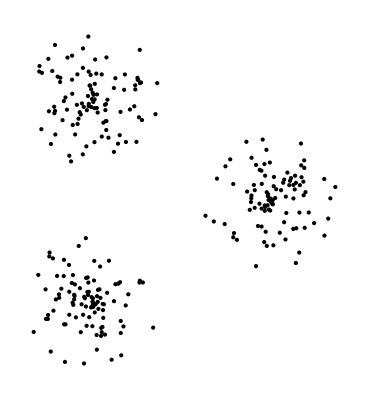

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[3,"class"],1]]]
```

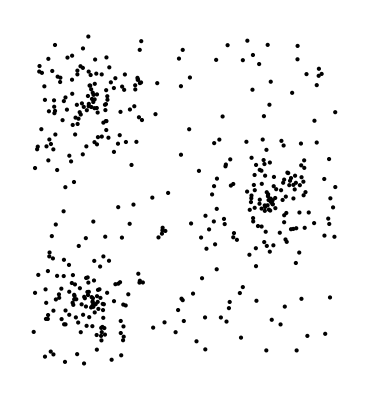

```mathematica
Graphics[Map[Point[#]&,Join[Flatten[samples[3,"class"],1],samples[3,"background"]]]]
```

```mathematica
samplesS[3]=ExportString[Join[Flatten[samples[3,"class"],1],samples[3,"background"]],"TSV"]<>"\n";
```

```mathematica
(*(samples[3,"All"]=Append[samples[3,"class"],samples[3,"background"]])//Length*)
```

4

全サンプルの平均半径

```mathematica
id=3
```

3

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-0.0140464,0.00237825}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.02263

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.983592,0.0162897},{-0.502691,0.851617},{-0.523039,-0.860772}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.290919,0.300218,0.272216}

```mathematica
Export["data3.tsv",strDataToExportStr[3],"String"]
```

data3.tsv

```mathematica
Export["data3.ans.totalR",totalR[id],"Table"]
```

data3.ans.totalR

```mathematica
Export["data3.ans.clRs",clRs[id],"Table"]
```

data3.ans.clRs

## 3D

### data 7 (chain)

```mathematica
anntS[7]="Model: double chain.\n"
```

Model: double chain.

```mathematica
dim[7]=3;
numClass[7]=2;
numSample[7]={150,150};
numBG[7]={0};
```

```mathematica
dimS[7]=StringJoin[Riffle[{ToString[dim[7]],ToString[numClass[7]],ToString[numSample[7]],ToString[numBG[7]]},"\t"],"\n"]
```

3	2	{150, 150}	{0}

```mathematica
centers[7]={{0,0,0},{1,0,0}}
```

{{0,0,0},{1,0,0}}

```mathematica
(*origins[6]={{0,0},{0,0},{0,0}}*)
```

```mathematica
centersS[7]=ExportString[centers[7],"TSV"]<>"\n"
```

0	0	0
1	0	0

```mathematica
samples[7,1]=Map[sPolarToxyz[#]&,Table[{1,Pi/2,ph},{ph,0,2Pi-2Pi/150,2Pi/150}]];
```

```mathematica
Map[Point[#]&,samples[7,1]]//Length
```

150

```mathematica
Map[Point[#]&,samples[7,1]]//Graphics3D
```

-Graphics3D-

```mathematica
samples[7,2]=Map[sPolarToxyz[#]&,Table[{1,th,0},{th,0,2Pi-2Pi/150,2Pi/150}]];
```

```mathematica
Map[Point[#]&,samples[7,2]]//Length
```

150

```mathematica
Map[Point[#]&,samples[7,2]]//Graphics3D
```

-Graphics3D-

```mathematica
(*(samples[7,"All"]=Join[samples[7,1],Map[#+centers[7][[2]]&,samples[7,2]]]//N)//Length*)
```

```mathematica
(samples[7,"class"]=List[samples[7,1],Map[#+centers[7][[2]]&,samples[7,2]]]//N)//Length
```

2

```mathematica
Map[Point[#]&,samples[7,"class"]]//Graphics3D
```

-Graphics3D-

```mathematica
samplesS[7]=ExportString[Flatten[samples[7,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=7
```

7

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{0.5,-2.7293×10^-18,2.96059×10^-18}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.06354

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{5.92119×10^-18,-5.4586×10^-18,0.},{1.,0.,5.92119×10^-18}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{1.,1.}

```mathematica
Export["data7.tsv",strDataToExportStr[7],"String"]
```

data7.tsv

```mathematica
Export["data7.ans.totalR",totalR[id],"Table"]
```

data7.ans.totalR

```mathematica
Export["data7.ans.clRs",clRs[id],"Table"]
```

data7.ans.clRs

## Many class

### data 8 (4 classes)

```mathematica
anntS[8]="Model: central random , circles, one radius, 2d-4class.\n"
```

Model: central random , circles, one radius, 2d-4class.

```mathematica
dim[8]=2;
numClass[8]=4;
numSample[8]={100,100,100,100};
numBG[8]={0};
```

```mathematica
dimS[8]=StringJoin[Riffle[{ToString[dim[8]],ToString[numClass[8]],ToString[numSample[8]],ToString[numBG[8]]},"\t"],"\n"]
```

2	4	{100, 100, 100, 100}	{0}

```mathematica
centers[8]={{2,2},{2,-2},{-2,2},{-2,-2}}
```

{{2,2},{2,-2},{-2,2},{-2,-2}}

```mathematica
centersS[8]=ExportString[centers[8],"TSV"]<>"\n"
```

2	2
2	-2
-2	2
-2	-2

```mathematica
distMean[8]=Tr[Flatten[distanceMat[centers[8]]//N]]/(numClass[8]^2-numClass[8])
```

4.55228

```mathematica
samples[8,"class"]=Table[Map[#+centers[8][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[8]/4}],RandomReal[{0,2Pi}]}],{numSample[8][[n]]}]],{n,numClass[8]}];
```

```mathematica
maxmin[8]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[8,"class"],1]]]
```

{{3.09951,-3.03178},{3.04307,-3.03279}}

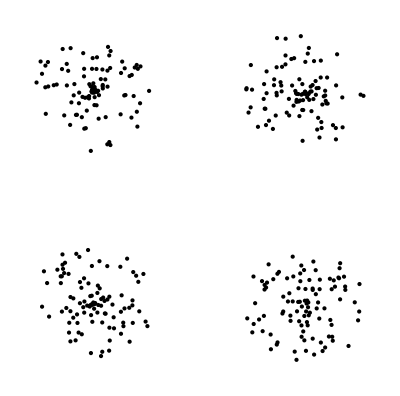

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[8,"class"],1]]]
```

```mathematica
samplesS[8]=ExportString[Flatten[samples[8,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=8
```

8

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-0.0063772,0.015729}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

2.82861

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{1.89961,1.96695},{1.98848,-2.00716},{-1.96367,2.04804},{-1.94993,-1.94491}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.542631,0.624339,0.524415,0.563449}

```mathematica
Export["data8.tsv",strDataToExportStr[8],"String"]
```

data8.tsv

```mathematica
Export["data8.ans.totalR",totalR[id],"Table"]
```

data8.ans.totalR

```mathematica
Export["data8.ans.clRs",clRs[id],"Table"]
```

data8.ans.clRs

### data 9 (8 classes)

```mathematica
anntS[9]="Model: central random , circles, one radius, 2d-8class.\n"
```

Model: central random , circles, one radius, 2d-8class.

```mathematica
dim[9]=2;
numClass[9]=8;
numSample[9]={100,100,100,100,100,100,100,100};
numBG[9]={0};
```

```mathematica
dimS[9]=StringJoin[Riffle[{ToString[dim[9]],ToString[numClass[9]],ToString[numSample[9]],ToString[numBG[9]]},"\t"],"\n"]
```

2	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[9]={{7,7},{7,-7},{-7,7},{-7,-7},{0,20},{20,0},{0,-20},{-20,0}}
```

{{7,7},{7,-7},{-7,7},{-7,-7},{0,20},{20,0},{0,-20},{-20,0}}

```mathematica
centersS[9]=ExportString[centers[9],"TSV"]<>"\n"
```

7	7
7	-7
-7	7
-7	-7
0	20
20	0
0	-20
-20	0

```mathematica
distMean[9]=Tr[Flatten[distanceMat[centers[9]]//N]]/(numClass[9]^2-numClass[9])
```

22.4998

```mathematica
samples[9,"class"]=Table[Map[#+centers[9][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[9]/4}],RandomReal[{0,2Pi}]}],{numSample[9][[n]]}]],{n,numClass[9]}];
```

```mathematica
maxmin[9]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[9,"class"],1]]]
```

{{24.7659,-25.5046},{24.9857,-25.3485}}

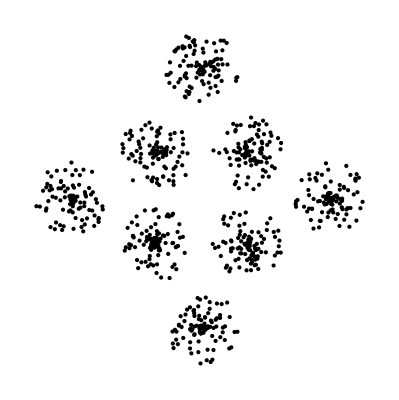

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[9,"class"],1]]]
```

```mathematica
samplesS[9]=ExportString[Flatten[samples[9,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=9
```

9

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-0.0279249,0.0825105}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

15.2418

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{7.54337,7.25903},{7.03716,-7.21853},{-7.08128,6.98331},{-7.27307,-6.68309},{-0.298978,20.3275},{19.8429,0.0133554},{0.0645102,-19.8406},{-20.058,-0.180962}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{2.80873,2.72457,2.83229,2.58195,3.09625,2.71146,2.63175,2.79678}

```mathematica
Export["data9.tsv",strDataToExportStr[9],"String"]
```

data9.tsv

```mathematica
Export["data9.ans.totalR",totalR[id],"Table"]
```

data9.ans.totalR

```mathematica
Export["data9.ans.clRs",clRs[id],"Table"]
```

data9.ans.clRs

### data 10 (3d-8 classes) (scale: base)

```mathematica
anntS[10]="Model: central random , circles, one radius, 3d-8class (base).\n"
```

Model: central random , circles, one radius, 3d-8class (base).

```mathematica
dim[10]=3;
numClass[10]=8;
numSample[10]={100,100,100,100,100,100,100,100};
numBG[10]={0};
```

```mathematica
dimS[10]=StringJoin[Riffle[{ToString[dim[10]],ToString[numClass[10]],ToString[numSample[10]],ToString[numBG[10]]},"\t"],"\n"]
```

3	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[10]=Tuples[{0,10},3]
```

{{0,0,0},{0,0,10},{0,10,0},{0,10,10},{10,0,0},{10,0,10},{10,10,0},{10,10,10}}

```mathematica
centersS[10]=ExportString[centers[10],"TSV"]<>"\n"
```

0	0	0
0	0	10
0	10	0
0	10	10
10	0	0
10	0	10
10	10	0
10	10	10

```mathematica
distMean[10]=Tr[Flatten[distanceMat[centers[10]]//N]]/(numClass[10]^2-numClass[10])
```

12.821

```mathematica
centers[10]
```

{{0,0,0},{0,0,10},{0,10,0},{0,10,10},{10,0,0},{10,0,10},{10,10,0},{10,10,10}}

```mathematica
samples[10,"class"]=Table[centers[10][[c]]+Table[RandomVariate[NormalDistribution[0,distMean[10]/16]],{3}],{c,numClass[10]},{100}];
```

```mathematica
maxmin[10]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[10,"class"],1]]]
```

{{12.2077,-2.23785},{12.3169,-2.28161},{12.3921,-2.51313}}

```mathematica
Graphics3D[Map[Point[#]&,Flatten[samples[10,"class"],1]]]
```

-Graphics3D-

```mathematica
samplesS[10]=ExportString[Flatten[samples[10,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=10
```

10

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{4.99516,4.98091,4.99445}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

8.71274

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.048113,0.118728,-0.0655771},{0.0261748,-0.0221942,9.93019},{-0.0611881,9.99308,0.0124593},{0.0223844,9.93769,10.0283},{10.1474,-0.0367061,-0.0080399},{9.8977,-0.0959738,9.89645},{9.97377,10.0129,0.0619213},{9.9069,9.93981,10.0999}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{1.32748,1.1927,1.22854,1.2895,1.34261,1.25043,1.24567,1.17958}

```mathematica
Export["data10.tsv",strDataToExportStr[10],"String"]
```

data10.tsv

```mathematica
Export["data10.ans.totalR",totalR[id],"Table"]
```

data10.ans.totalR

```mathematica
Export["data10.ans.clRs",clRs[id],"Table"]
```

data10.ans.clRs

### data 10.2 (3d-8 classes) (scale: 2)

```mathematica
anntS[10.2]="Model: central random , circles, one radius, 3d-8class, scaled.\n"
```

Model: central random , circles, one radius, 3d-8class, scaled.

```mathematica
dim[10.2]=3;
numClass[10.2]=8;
numSample[10.2]={100,100,100,100,100,100,100,100};
numBG[10.2]={0};
```

```mathematica
dimS[10.2]=StringJoin[Riffle[{ToString[dim[10.2]],ToString[numClass[10.2]],ToString[numSample[10.2]],ToString[numBG[10.2]]},"\t"],"\n"]
```

3	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[10.2]=Tuples[{0,10},3]/4//N
```

{{0.,0.,0.},{0.,0.,2.5},{0.,2.5,0.},{0.,2.5,2.5},{2.5,0.,0.},{2.5,0.,2.5},{2.5,2.5,0.},{2.5,2.5,2.5}}

```mathematica
centersS[10.2]=ExportString[centers[10.2],"TSV"]<>"\n";
```

```mathematica
distMean[10.2]=Tr[Flatten[distanceMat[centers[10.2]]//N]]/(numClass[10.2]^2-numClass[10.2])
```

3.20525

```mathematica
samples[10.2,"class"]=Table[centers[10.2][[c]]+Table[RandomVariate[NormalDistribution[0,distMean[10.2]/10]],{3}],{c,numClass[10.2]},{100}];
```

```mathematica
maxmin[10.2]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[10.2,"class"],1]]]
```

{{3.42294,-0.901513},{3.52321,-1.26508},{3.36728,-0.89493}}

```mathematica
Graphics3D[Map[Point[#]&,Flatten[samples[10.2,"class"],1]]]
```

-Graphics3D-

```mathematica
samplesS[10.2]=ExportString[Flatten[samples[10.2,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=10.2
```

10.2

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{1.24555,1.25744,1.25214}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

2.23728

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{-0.00696225,-0.000607492,0.0276816},{0.0270022,0.00396486,2.50724},{0.00123084,2.54725,0.032494},{-0.0706133,2.49776,2.51912},{2.49144,-0.06058,-0.0453283},{2.52223,-0.0125023,2.51641},{2.5355,2.5219,-0.0447696},{2.46459,2.56233,2.50424}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.502216,0.53903,0.464166,0.542735,0.501598,0.5437,0.514467,0.488938}

```mathematica
Export["data10-2.tsv",strDataToExportStr[10.2],"String"]
```

data10-2.tsv

```mathematica
Export["data10-2.ans.totalR",totalR[id],"Table"]
```

data10-2.ans.totalR

```mathematica
Export["data10-2.ans.clRs",clRs[id],"Table"]
```

data10-2.ans.clRs

### data 10.3 (3d-8 classes) (scale: 3)

```mathematica
anntS[10.3]="Model: central random , circles, one radius, 3d-8class, scaled(3).\n"
```

Model: central random , circles, one radius, 3d-8class, scaled(3).

```mathematica
dim[10.3]=3;
numClass[10.3]=8;
numSample[10.3]={100,100,100,100,100,100,100,100};
numBG[10.3]={0};
```

```mathematica
dimS[10.3]=StringJoin[Riffle[{ToString[dim[10.3]],ToString[numClass[10.3]],ToString[numSample[10.3]],ToString[numBG[10.3]]},"\t"],"\n"]
```

3	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[10.3]=Tuples[{0,10},3]/8//N
```

{{0.,0.,0.},{0.,0.,1.25},{0.,1.25,0.},{0.,1.25,1.25},{1.25,0.,0.},{1.25,0.,1.25},{1.25,1.25,0.},{1.25,1.25,1.25}}

```mathematica
centersS[10.3]=ExportString[centers[10.3],"TSV"]<>"\n"
```

0.	0.	0.
0.	0.	1.25
0.	1.25	0.
0.	1.25	1.25
1.25	0.	0.
1.25	0.	1.25
1.25	1.25	0.
1.25	1.25	1.25

```mathematica
distMean[10.3]=Tr[Flatten[distanceMat[centers[10.3]]//N]]/(numClass[10.3]^2-numClass[10.3])
```

1.60262

```mathematica
samples[10.3,"class"]=Table[centers[10.3][[c]]+Table[RandomVariate[NormalDistribution[0,distMean[10.3]/10]],{3}],{c,numClass[10.3]},{100}];
```

```mathematica
maxmin[10.3]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[10.3,"class"],1]]]
```

{{1.7384,-0.477428},{1.64395,-0.381094},{1.68027,-0.488302}}

```mathematica
Graphics3D[Map[Point[#]&,Flatten[samples[10.3,"class"],1]]]
```

-Graphics3D-

```mathematica
samplesS[10.3]=ExportString[Flatten[samples[10.3,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=10.3
```

10.3

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{0.63313,0.625889,0.619219}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.10225

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{-0.00700958,0.0198909,-0.00906769},{-0.000884188,-0.0165617,1.24505},{0.0155199,1.23328,-0.0130133},{0.0192473,1.25866,1.21962},{1.2593,0.00797512,0.0219774},{1.24177,-0.00954736,1.24405},{1.2611,1.27383,0.00917308},{1.276,1.23958,1.23595}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.247222,0.237389,0.236749,0.245979,0.255724,0.246013,0.253914,0.263704}

```mathematica
Export["data10-3.tsv",strDataToExportStr[10.3],"String"]
```

data10-3.tsv

```mathematica
Export["data10-3.ans.totalR",totalR[id],"Table"]
```

data10-3.ans.totalR

```mathematica
Export["data10-3.ans.clRs",clRs[id],"Table"]
```

data10-3.ans.clRs

### data 10.4 (3d-8 classes) (scale: 4)

```mathematica
id=10.4
```

10.4

```mathematica
anntS[id]="Model: central random , circles, one radius, 3d-8class, scaled(4).\n"
```

Model: central random , circles, one radius, 3d-8class, scaled(4).

```mathematica
dim[id]=3;
numClass[id]=8;
numSample[id]={100,100,100,100,100,100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

3	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[id]=Tuples[{0,10},3]/8//N
```

{{0.,0.,0.},{0.,0.,1.25},{0.,1.25,0.},{0.,1.25,1.25},{1.25,0.,0.},{1.25,0.,1.25},{1.25,1.25,0.},{1.25,1.25,1.25}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

0.	0.	0.
0.	0.	1.25
0.	1.25	0.
0.	1.25	1.25
1.25	0.	0.
1.25	0.	1.25
1.25	1.25	0.
1.25	1.25	1.25

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]//N]]/(numClass[id]^2-numClass[id])
```

1.60262

```mathematica
samples[id,"class"]=Table[centers[id][[c]]+Table[RandomVariate[NormalDistribution[0,distMean[id]/15]],{3}],{c,numClass[id]},{100}];
```

```mathematica
maxmin[id]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[id,"class"],1]]]
```

{{1.51787,-0.256816},{1.52846,-0.25376},{1.55922,-0.341474}}

```mathematica
Graphics3D[Map[Point[#]&,Flatten[samples[id,"class"],1]]]
```

-Graphics3D-

```mathematica
samplesS[id]=ExportString[Flatten[samples[id,"class"],1],"TSV"]<>"\n";
```

全サンプルの平均半径

```mathematica
id=10.4
```

10.4

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{0.627653,0.621217,0.620682}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.09848

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.0174134,0.00435305,-0.00903742},{-0.00697142,-0.0278468,1.24435},{-0.0069758,1.24051,-0.0254552},{-0.00503453,1.24191,1.23715},{1.24862,-0.00706476,0.00624928},{1.25543,0.0134639,1.25513},{1.25634,1.25945,-0.0103995},{1.26241,1.24496,1.26747}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.164716,0.163577,0.170566,0.16596,0.167984,0.177276,0.180335,0.179377}

```mathematica
Export["data10-4.tsv",strDataToExportStr[id],"String"]
```

data10-4.tsv

```mathematica
Export["data10-4.ans.totalR",totalR[id],"Table"]
```

data10-4.ans.totalR

```mathematica
Export["data10-4.ans.clRs",clRs[id],"Table"]
```

data10-4.ans.clRs

## high Dimensional

## Experimental